# VE401 Final Review

## Fisher’s Hypothesis Test

### Hypotheses and Testing

Example: I am a soft drink manufacturer. You are a seller and want to buy my products. I claim that my product has μ≥500ml. You don’t trust me and sampled 20 bottles from my batch.

```mathematica
Data=RandomVariate[NormalDistribution[499,2],20]
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

```mathematica
Mean[Data]
```

499.115

I claim that the samples are too “extreme” and you are picking bottles with small volumes by chance. Actually, more and more have larger volume. Would you believe me?

Steps:

Figure out the parameter θ and the null value θ_0 you are testing. (θ=μ,θ_0=500 in my example)

Set up a null hypothesis H_0. It can be one of the following: (μ≥500 in my example)

θ=θ_0.

θ≤θ_0.

θ≥θ_0.

Figure out the distribution of the estimator of θ and thus the test statistics. ((X̄-μ)/(σ/√n) follows standard normal distribution. We take Z=(X̄-μ)/(σ/√n) as test statistics)

Analyze data, calculate P-value to see if there is enough evidence of reject H_0.

### Significance or P-value for One-Tailed Test

Intuition: How likely will we observe the data if what I claim is true? How “extreme” is the data? P=P[getting this or even more "extreme" observation|H_0 is true].

Mathematical representation: Denoting the sample statistics of θ̂ as k, we have

P value=Piecewise[{{P[θ̂≤k|θ=θ_0], if null hypothesis is H_0:θ≥θ_0}, {P[θ̂≥k|θ=θ_0], if null hypothesis is H_0:θ≤θ_0}}]

Example:

##### What is the P-value for my claim that μ≥500ml? Assume that we know true variance σ^2=4 ml^2 and sample statistics X̄=499.115 ml.

For H_0:μ≥500, we calculate (suppose we already know that σ=2).

P[getting more "extreme" observation|H_0 is true]=P[X̄≤ 499.115|μ≥500, σ=2]
   <=P[X̄≤ 499.115|μ=500, σ=2]
=P[(X̄-500)/(2/√20)≤(499.115-500)/(2/√20) ]
=P[Z≤-1.978]
=0.024

```mathematica
CDF[NormalDistribution[],(Mean[Data]-500)/(2/√20)]
```

0.0239544

So, there is at most 2.4% chance to obtain such “extreme” data if my claim is true. Since it is small, so we reject H_0 at the 2.4% level of significance.

### Significance or P-value for Two-Tailed Test

Mathematical representation: Denoting the sample statistics of θ̂ as k, we have

P value=P[|θ̂-θ_0|≥|k-θ_0| |θ=θ_0]  | if null hypothesis is H_0:θ=θ_0

Example:

##### What is the P-value if my claim is μ=500ml? Assume that we know true variance σ^2=4 ml^2 and sample statistics X̄=499.115 ml.

For H_0:μ≥500, we calculate (suppose we already know that σ=2).

P[getting more "extreme" observation|H_0 is true]=P[|X̄-500|≥| 499.115-500||μ=500, σ=2]
   =2P[X̄≤ 499.115|μ=500, σ=1]
=0.048

So, there is at most 4.8% chance to obtain such “extreme” data if my claim is true. Since it is small, so we reject H_0 at the 4.8% level of significance.

## Neyman-Pearson Decision Theory

### Hypotheses and Testing

Steps:

Figure out the parameter θ and the null value θ_0 you are testing.

We set up two competing hypotheses H_0 and H_1. (e.g. H_0:μ≥500, H_1:μ≤499). They can be one of the following: for some δ>0,

H_0:θ=θ_0, H_1:|θ-θ_0|≥δ.

H_0:θ≤θ_0, H_1:θ≥θ_0+δ.

H_0:θ≥θ_0, H_1:θ≤θ_0-δ .

Decide α and β. Calculate the critical region and the sample size.

Analyze data. If the sample statistics lies in the interval of H_1, we accept H_1. Otherwise, we see the whether the sample statistics lies in the critical region. If yes, then reject H_0.

### Type I and Type II Errors

Intuition: Type I error is the case when my claim is falsely rejected. Type II error is the case when my claim is falsely accepted.

|  | In fact | 
 |  | H_0 true | H_0 false
Our choice | Accept H_0 | Good | Type II error
 | Reject H_0 | Type I error | Good

### α and Critical Region

Definition: α=P[Type I error]. The critical region is the interval such that if H_0 is true, the probability of statistics falling into the interval (letting us to reject H_0) is at most α. In other words, the complement of critical region is a 100(1-α)% confidence interval for the parameter.

Usage: If P value≤α, we reject H_0. If sample statistics lies in the critical region, we reject H_0.

Example:

##### We set α=0.05. Calculate the critical region for H_0:μ≥500ml. Assume that we know true variance σ^2=4 ml^2. According to the critical region, should we reject H_0?

We want Z=(X̄-μ_0)/(σ/√n)<-z_0.05 to reject H_0. The critical region is then (-∞,μ_0-z_0.05 σ/(√n))=(-∞,499.264). Since our data X̄=499.115 lies in the critical region, we reject H_0.

```mathematica
Subscript[z, α_]:=InverseCDF[NormalDistribution[],1-α];
500-(2 Subscript[z, 0.05])/(√20)
```

499.264

### β and Sample Size

Definition: β=P[Type II error]=P[Sample statistics lies outside critical region|H_1 true].

Usage:

To calculate a good sample size. n≈((z_(α/2)+z_β)^2 σ^2)/δ^2.

To calculate the power of a test. power=1-β. A powerful test needs smaller sample size, and is more likely to reject H_0.

To plot the OC curve, or β vs. d curve, so that we find n more easily. Here

d=Piecewise[{{(|μ-μ_0|)/σ, if H_0:μ=μ_0}, {(μ-μ_0)/σ, if H_0:μ≤μ_0}, {-(μ-μ_0)/σ, if H_0:μ≥μ_0}}]

Examples:

##### What is the power of my test given that the true mean μ=499ml, true variance σ^2=4 ml^2 and the sample size n=20?

We have d=(|499-500|)/2=0.5,n=20. According to the OC Curve, β≈0.3. So the power is approximately 0.7. So the test is not powerful enough.

##### If the true mean of my product has volume μ=499ml, and the variance is σ^2=4 ml^2, what sample size do we need to get a power of 0.8, if we set α=0.05?

We have d=(|499-500|)/2=0.5. We will need about 30 samples to get a power of 0.8.

```mathematica
((Subscript[z, 0.05]+Subscript[z, 0.2])^2 4)/(499-500)^2
```

24.7302

##### Plot the OC Curve of the test of my product, given α=0.05, sample size n=20 and the variance σ^2=4 ml^2.

In my case H_0:μ≥500, H_1:μ≤499, we need to calculate

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[X̄>499.264|(μ_0-μ)/σ=d]
<=P[X̄>499.264|μ=500-2 d]
=P[(X̄-(500-2d))/(2/√20)>(499.264-(500-2d))/(2/√20)]
=P[Z>(499.264-(500-2d))/(2/√20)]

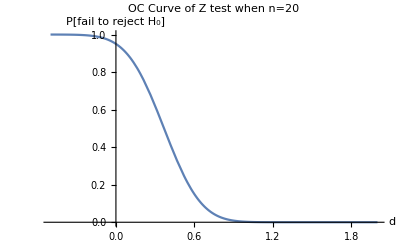

```mathematica
Plot[1-CDF[NormalDistribution[],(499.264-(500-2d))/(2/√20)],{d,-.5,2},AxesLabel->{"d","P[fail to reject H_0]"}, PlotLabel->"OC Curve of Z test when n=20"]
```

When d=0, we can see that β=1-α=0.95.

##### How large should the true mean μ differ from μ_0=500ml so that H_0 is rejected 90% of the time (given H_1 is true)?

According to the OC Curve, at d≈0.65 we obtain β=0.1 or a power of 0.9. This means we need (μ_0-μ)/σ=(500-μ)/2>0.65⇒μ<498.7.

## Null Hypothesis Significance Tests (NHST)

### Hypotheses and Testing

Steps:

Figure out the parameter θ and the null value θ_0 you are testing.

We set up two competing hypotheses H_0 and H_1. (e.g. H_0:μ≥500, H_1:μ≤499). They can be one of the following: for some δ>0,

H_0:θ=θ_0, H_1:θ≠θ_0.

H_0:θ≤θ_0, H_1:θ>θ_0.

H_0:θ≥θ_0, H_1:θ<θ_0.

Decide α.

Analyze data. Calculate the P-value and see if there is enough evidence to reject H_0.

Note: NHST is biased against failing to reject H_0 (too easy to reject H_0).

## Single Sample Tests and Comparison of Parameter

### Test Statistics

From now on, you will learn a lot of tests. For each test, you need to pay attention to:

What parameter are we testing?

What parameter do we know?

What is the distribution of test statistics?

Denoting the distribution of test statistics as 𝒟, and 𝒹_α as the number such that ∫_(-∞)^𝒹_α f_𝒟(x)ⅆx=1-α, we reject at significance level α,

H_0:θ=θ_0 if 𝒟>𝒹_(α/2) or 𝒟<𝒹_(1-α/2). (Test statistics is too small or too big)

H_0:θ≤θ_0 if 𝒟>𝒹_α. (Test statistics is too big)

H_0:θ≥θ_0 if 𝒟<𝒹_(1-α). (Test statistics is too small)

### Single Sample Tests for Mean (Z-Test and T-Test)

Testing 
Parameter | Distribution of X_i | Variance  σ | Sample Size n | Test Statistics | OC Curve x-axis
(for two sided test)
μ | normal | known | any | Z=(X̄-μ_0)/(σ/√n) | d=(|μ-μ_0|)/σ
 | any | known | large |  | 
 | any | unknown | large | Z=(X̄-μ_0)/(S/√n) | d=(|μ-μ_0|)/S
 | normal | unknown | small | T_(n-1)=(X̄-μ_0)/(S/√n) |

Example:

##### If the true variance is unknown, what is the power of my T-test if the true mean is μ=499ml?

```mathematica
(500-499)/(√Variance[Data])
```

0.462933

The corresponding power is about 1-0.35=0.65.

### Single Sample Tests for Variance (Chi-Squared Test)

Testing Parameter | Distribution of X_i | Test Statistics | OC Curve x-axis
(for two sided test)
σ | Normal | χ_(n-1)^2=((n-1)S^2)/σ_0^2 | λ=σ/σ_0

### Single Sample Tests for Median (Non-Parametric)å

#### Sign Test for the Median

Testing Parameter | Distribution of X_i | Test Statistics
M | any | Binomial_(n,0.5)=Q_+

where Q_+ is the number of data that lies above M_0. (Usually the data equal to M_0 is discarded).

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Test the hypothesis H_0:M≥500ml.

We can count that Q_+=7. P[Q_+≤7]=1/2^20∑_(i=0)^7 (20
i)=0.13. There is no enough evidence to reject H_0.

#### Wilcoxon Signed Rank Test

Testing Parameter | Distribution of X_i | Test Statistics
M | symmetric | W_+

where W_+ is the sum of the positive ranks when ranking |X_i-M_0|. When there is a tie, we take the average value. For example, if the first, second and third smallest |X_i-M_0|  is a group of 3 ties, we rank them all as (1+3)/2=2.
For small n, you can refer to a table of critical values here: http://users.stat.ufl.edu/~winner/tables/wilcox_signrank.pdf. For n≥10, we can approximate the test statistics with E[W]=(n(n+1))/4, Var[W]=(n(n+1)(2n+1))/24. For each group of t ties, the variance is reduced by (t^3-t)/48.

```mathematica
Sort[Data-500]
```

{-4.48438,-3.92626,-3.10595,-2.9944,-2.86761,-2.34263,-1.98916,-1.91898,-1.55252,-1.12854,-1.1048,-0.281418,-0.271902,0.156908,0.356726,0.930833,1.13896,1.89039,2.17724,3.62415}

##### Test the hypothesis H_0:M≥500ml.

We can count that W_+=1+4+5+8+10+13+18=59. According to the table, the critical value for α=0.05 is 60. Since 59<60 we are able to reject H_0 with P<0.05.

```mathematica
Needs["HypothesisTesting`"]
SignedRankTest[Data,500,"TestDataTable",AlternativeHypothesis->"Less"]
```

| Statistic | P-Value
Signed-Rank | 59. | 0.0446939

### Estimation of Proportion

For a Bernoulli random variable X_i, we can calculate p̂=X̄=1/n∑_(i=1)^n x_i. The confidence interval for p would be

p̂±z_(α/2)√(p̂(1-p̂)/n)

If we want to test that |p-p̂|<d for some d>0 with 100(1-α)% confidence, we need the sample size to be at least

n=(z_(α/2)^2 p̂(1-p̂))/d^2≤(z_(α/2)^2)/(4 d^2)

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Give a 95% confidence interval of the proportion of good product (with volume ≥500ml) in my batch.

We have p̂=7/20=0.35 and n=20. A confidence interval would be 0.35±0.21.

### Single Sample Test of Proportion (Z-Test)

According to central limit theorem, p̂ is approximately normally distributed with mean p and variance p(1-p)/n.

Testing Parameter | Distribution of X_i | Sample Size | Test Statistics
p | Bernoulli | large | Z=(p̂-p_0)/(√(p_0(1-p_0)/n))

### Comparing Two Proportions (Z-Test, Pooled Test)

Testing Parameter | Distribution of X_i | Sample Size | Hypothesis H_0 | Test Statistics
p_1-p_2 | Bernoulli | large | |p_1-p_2|≥d
for some d>0 | Z=((p̂)_1-(p̂)_2-(p_1-p_2)_0)/(√(((p̂)_1(1-(p̂)_1))/n_1+((p̂)_2(1-(p̂)_2))/n_2))
 |  |  | p_1=p_2 | Z=((p̂)_1-(p̂)_2)/(√(p̂(1-p̂)(1/n_1+1/n_2)))
where p̂=(n_1(p̂)_1+n_2(p̂)_2)/(n_1+n_2)

### F Distribution

Purpose: To describe the distribution of the ratio of two scaled chi-squared random variables.

Mathematical representation: F_(γ_1,γ_2)=(χ_γ_1^2/γ_1)/(χ_γ_2^2/γ_2)is said to follow an F-distribution with γ_1 and γ_2 degrees of freedom.

Properties:

P[F_(γ_1,γ_2)<x]=1-P[F_(γ_2,γ_1)<1/x].

f_(1-α,γ_1,γ_2)=1/(f_(α,γ_2,γ_1)).

```mathematica
P[1/x<F<x]=P[F<x]-P[F<1/x]=P[F<x]-
```

```mathematica
CDF[FRatioDistribution[4,5],1]
```

BetaRegularized[4/9,2,5/2]

### Comparing Two Variance (F-Test)

Testing Parameter | Distribution of X_i | Test Statistics | Hypothesis H_0 | OC Curve x-axis
(forn_1=n_2=n)
σ_1/σ_2 | Normal | F_(n_1-1,n_2-1)=S_1^2/S_2^2 | σ_1/σ_2≥1
σ_1/σ_2≤1
σ_1/σ_2=1 | λ=σ_1/σ_2

Example:

##### Plot the OC Curve For F-test for sample sizes n_1, n_2.

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[f_(0.975,n_1-1,n_2-1)<S_1^2/S_2^2<f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[(1/σ_1^2)/(1/σ_2^2)f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<(1/σ_1^2)/(1/σ_2^2)f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<1/λ^2 f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<F_(n_1-1,n_2-1)<1/λ^2 f_(0.025,n_1-1,n_2-1)]

One nice property for this β=f(λ) curve is f(λ)=f(1/λ).

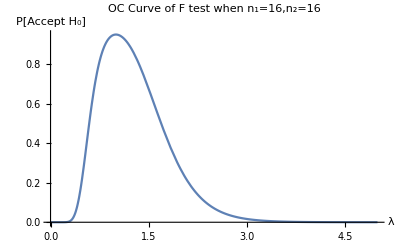

```mathematica
Subscript[n, 1]=16;Subscript[n, 2]=16;
f[λ_]:=CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.975]]-CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.025]];
Plot[f[λ],{λ,0,5},PlotLabel->"OC Curve of F test when n_1="<>ToString[Subscript[n, 1]]<>",n_2="<>ToString[Subscript[n, 2]],AxesLabel->{"λ","P[Accept H_0]"}]
```

### Comparing Two Means (Z-test, Pooled/Paired T-test)

Example: I am a soft drink manufacturer and I have two machines that produce bottles of soft drink. I would like to know if there is a difference in the products of the two machines. I sampled 10 bottles from each of the two machines.

```mathematica
Data1=RandomVariate[NormalDistribution[499,2],10]
Data2=RandomVariate[NormalDistribution[500,2],10]
```

{500.225,497.209,502.43,499.553,498.25,498.235,498.463,496.606,498.849,498.312}

{500.439,497.685,498.616,499.87,501.796,500.566,499.231,497.896,499.774,498.836}

```mathematica
Mean[Data1]
Mean[Data2]
```

498.813

499.471

```mathematica
√Variance[Data1]
√Variance[Data2]
```

1.63617

1.27599

I would like to test H_0:μ_1≥μ_2, and H_1:μ_1≤μ_2-1.

Testing 
Parameter | Distribution 
of the two RVs | Sample size
n_1,n_2 | Variance
σ_1^2, σ_2^2 | Test Statistics | OC curve x-axis
(for two-tailed test)
μ_1-μ_2 | Normal | any | known | Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(σ_1^2/n_1+σ_2^2/n_2)) | d=(|μ_1-μ_2|)/(√(σ_1^2+σ_2^2)) where
n=(σ_1^2+σ_2^2)/(σ_1^2/n_1+σ_2^2/n_2)
 |  | large | unknown | Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_1^2/n_1+S_2^2/n_2)) | 
 |  | small | unknown with
σ=σ_1=σ_2 | T_(n_1+n_2-2)=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))
where S_p^2=((n_1-1)S_1^2+(n_2-1)S_2^2)/(n_1+n_2-2) | In case of n=n_1=n_2, 
d=(|μ_1-μ_2|)/(2σ)
where we use modified 
sample size n^*=2n-1,
and σ can be estimated.
 |  | small | unknown | T_γ=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_1^2/n_1+S_2^2/n_2)) where
γ=((S_1^2/n_1+S_2^2/n_2)^2)/(((S_1^2/n_1)^2)/(n_1-1)+((S_2^2/n_2)^2)/(n_2-1)) (we take
the floor) | No simple OC Curves

When variances are unknown, current recommendations are to always use Welch’s test.

##### Suppose I know that σ_1=σ_2=2, which test would you use? What is the test statistics?

The Z-test with known variance. The test statistics is Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(σ_1^2/n_1+σ_2^2/n_2))=(498.813-499.471)/(√(8/10))=-0.73. This gives us a P-value of 0.23. This is large, so we failed to reject H_0.

```mathematica
CDF[NormalDistribution[],(Mean[Data1]-Mean[Data2])/(√(8/10))]
```

0.230966

##### Suppose we don’t know about the true variance, but suppose we know they are equal. which test would you use? What is the test statistics?

The T-test with equal variance. We have pooled variance S_p^2=((n_1-1)S_1^2+(n_2-1)S_2^2)/(n_1+n_2-2)=(9(1.64)^2+9(21.28)^2)/18=2.15, so the test statistics is T_(10+10-2)=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))=(498.813-499.471)/(√(2.15×2/19))=-1.0. This gives us a P-value of 0.16. So there is no evidence to reject H_0.

```mathematica
CDF[StudentTDistribution[18],(Mean[Data1]-Mean[Data2])/(√((Variance[Data1]+Variance[Data2])/2 2/10))]
```

0.1646152521384

```mathematica
√Variance[Data1]
√Variance[Data2]
```

1.63617

1.27599

##### Suppose we know that μ_1=499,μ_2=500. What is the power of the T-test for unknown variance if α=0.05?

We can use the estimated variance S_p^2=2.15, and calculate d=(μ_2-μ_1)/(2σ)≈1/(2 √2.15)=0.34. Choosing n^*=2n-1=19≈20, we get a β of approximately 0.56, so the power is approximately 0.44.

##### Suppose we don’t know anything about the true variance. which test would you use? What is the test statistics?

Welch’s T-test with unknown variance. We have the degrees of freedom γ=⌊((S_1^2/n_1+S_2^2/n_2)^2)/(((S_1^2/n_1)^2)/(n_1-1)+((S_2^2/n_2)^2)/(n_2-1))⌋=16. T_16=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))=-1.0. This gives us again a P-value of 0.17. So there is no evidence to reject H_0.

```mathematica
Floor[(Variance[Data1]/10+Variance[Data2]/10)^2/((Variance[Data1]/10)^2/9+(Variance[Data2]/10)^2/9)]
```

16

### Comparing Locations (Non-parametric)

Testing Parameter | Distribution of X,Y | Sample Size | Hypothesis H_0 | Test Statistics
P[X>Y] | continuous | m samples of X
n samples of Y
m≤n. | P[X>Y]=1/2
P[X>Y]≥1/2
P[X>Y]≤1/2 | W_m

### Test for Mean of Difference of two RVs (Paired T - test)

Testing Parameter | Distribution of (X,Y) | Sample Size | Test Statistics
μ_D
where D=X-Y | joint bivariate
normal distribution | n=n_X=n_Y | T_(n-1)=(D̄-(μ_D)_0)/(√(S_D^2/n))
M_D
where  D=X-Y | independent, same distribution
but different location (D symmetric) | any | W_+ (Wilcoxon
signed rank statistics)

### Comparison Between Pooled and Paired

Testing Parameter | Distribution of (X,Y) | Test Statistics
μ_X-μ_Y | joint bivariate
normal distribution
 | T_(2n-2)=(X̄-Ȳ)/(√(2S_p^2/n))    where S_p^2=(S_1^2+S_2^2)/2
 |  | T_(n-1)=(D̄-(μ_D)_0)/(√(S_D^2/n))
When the test statistics is the same,pooledT-test is more powerful because of more degrees of freedom.

### Single Sample Test for Correlation Coefficient (Z - test)

Testing Parameter | Sample Size | Test Statistics
ρ | large |  Z=(√(n-3))/2 (ln((1+R)/(1-R))-ln((1+ρ_0)/(1-ρ_0)))=√(n-3)(artanh(R)-artanh(ρ_0))

The 100(1-α)% confidence interval for ρ is tanh(artanh(R)±(z_(α/2))/(√(n-3)))

## Linear Regression

### If you want to perform simple linear regression, use the code below:

```mathematica
X= {1,1,3.3,3.3,4,4,4,5.6,5.6,5.6,6,6,6.5,6.5}
Y={1.6,1.8,1.8,2.7,2.6,2.6,2.2,3.5,2.8,2.1,3.4,3.2,3.4,100}
```

{1,1,3.3,3.3,4,4,4,5.6,5.6,5.6,6,6,6.5,6.5}

{1.6,1.8,1.8,2.7,2.6,2.6,2.2,3.5,2.8,2.1,3.4,3.2,3.4,100}

```mathematica
n= Length[X];
X2 =(X)^2;
Y2 = (Y)^2;
XY = X.Y;
Sxx=Total[X2]-n*(Mean[X]^2);
Syy=Total[Y2]-n*(Mean[Y]^2);
Sxy =Total[XY] -n*Mean[X]*Mean[Y];
b1 = Sxy/Sxx ;
b0 = Mean[Y]-b1*Mean[X];
SSE = Syy-b1*Sxy;
R2 = Sxy^2 /(Sxx*Syy);
S =Sqrt[ SSE/(n-2)];
```

Or just use the function MMA provides:

```mathematica
data={{0,1},{1,0},{3,2},{5,4}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[0.186441+0.694915 x]

```mathematica
Normal[lm]
```

0.186441+0.694915 x

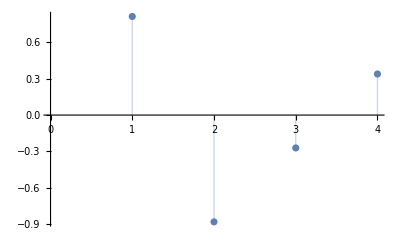

```mathematica
ListPlot[lm["FitResiduals"], Filling->Axis]
```

### Lack of Fit: Error Sum of Squares pure error and lack of fit -Graphics--Graphics-

Taking example from slide 666 - 667-Graphics-

```mathematica
SSEpe=6.453;
Syy=66.6437;
Sxy=154;
b1=0.051;
```

```mathematica
SSE=Syy−b1*Sxy
```

58.7897

```mathematica
SSElf=SSE−SSEpe
```

52.3367

Here F k−2;n−k, k-2=3 and n-k=10

```mathematica
F=(SSElf/(3))/(SSEpe/(10))
```

27.0348

```mathematica
InverseCDF[FRatioDistribution[3,10],0.95]
```

3.70826

Based on the F3;10 distribution, we can reject H0 with P < 0.05 (f0.05;3;10 = 3.708). There is evidence that a linear regression model is not appropriate

### Confidence and Prediction Intervals

```mathematica
X={100,120,140,160,180};
Y={45,54,66,74,85};
n= Length[X];
X2 =(X)^2;
Y2 = (Y)^2;
XY = X.Y;
Sxx=Total[X2]-n*(Mean[X]^2);
Syy=Total[Y2]-n*(Mean[Y]^2);
Sxy =Total[XY] -n*Mean[X]*Mean[Y];
b1 = Sxy/Sxx ;
b0 = Mean[Y]-b1*Mean[X];
SSE = Syy-b1*Sxy;
R2 = Sxy^2 /(Sxx*Syy);
S =Sqrt[ SSE/(n-2)];
Data = Transpose[{X,Y}];
model = LinearModelFit[Data,x,x];
alpha =0.05;
t=InverseCDF[StudentTDistribution[n-2],alpha/2];
conf = model["MeanPredictionBands",ConfidenceLevel->1-alpha]/.x->130 ;
pred= model["SinglePredictionBands",ConfidenceLevel->1-alpha]/.x->130 ;
Print["Band for b1: ",b1+t*S/Sqrt[Sxx]," to " ,b1-S/Sqrt[Sxx]]
Print["Band for b0: ",b0+t*(S*Sqrt[Total[X2]])/Sqrt[n*Sxx]," to ",b0-t*(S*Sqrt[Total[X2]])/Sqrt[n*Sxx]]
```

LinearModelFit::dpbss: The number of unique basis functions is 4 fewer than the number of basis functions specified in {100,120,140,160,180}. Duplicated basis functions will be removed.

LinearModelFit::ivar: {100,120,140,160,180} is not a valid variable.

LinearModelFit::ivar: {130} is not a valid variable.

Band for b1: 0.451387 to 1/2-(√(7/3))/100

Band for b0: -12.1433 to 1.74328

### Multiple Linear Regression

```mathematica
X=({{0.5, 5}, {1, 4}, {1.5, 3}, {2, 2}, {2.5, 1}});
y=({{-0.51}, {-2.09}, {-6.03}, {-9.28}, {-17.12}});
b = Inverse[Transpose[X].X].Transpose[X].y
```

{-6.37633,0.852833}

### F-Test for Significance of Regression

```mathematica
m = LinearModelFit[{X,y}];
m
p = 2;
n=5;
FStatistics = (n-p-1)/p m["RSquared"]/(1-m["RSquared"])
```

FittedModel[-6.37633 #1+0.852833 #2]

35.5873

### Confidence Interval

```mathematica
m["ParameterConfidenceIntervalTable",ConfidenceLevel->.90]
```

| Estimate | Standard Error | Confidence Interval
#1 | -6.37633 | 0.684035 | {-7.98612,-4.76655}
#2 | 0.852833 | 0.342017 | {0.047942,1.65772}

```mathematica
m["ParameterConfidenceIntervalTable",ConfidenceLevel->.95]
```

| Estimate | Standard Error | Confidence Interval
#1 | -6.37633 | 0.684035 | {-8.55324,-4.19943}
#2 | 0.852833 | 0.342017 | {-0.235619,1.94129}

### T-Test for the Model Parameters

See slide 731